Look at version 7.9 through 7.12...

```mathematica
Needs["NasaCdf`"]
```

```mathematica
dir=FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"TestFiles"}]
```

/Users/john/src/chaos/TestFiles

```mathematica
files=FileNames[__~~"C7L"~~__~~".cdf",dir<>"/out",Infinity]
```

{/Users/john/src/chaos/TestFiles/out/7.10/SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf,/Users/john/src/chaos/TestFiles/out/7.11/SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf,/Users/john/src/chaos/TestFiles/out/7.12/SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf,/Users/john/src/chaos/TestFiles/out/7.9/SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf}

```mathematica
versions=FileNameTake[#,{-2}]&/@files
```

{7.10,7.11,7.12,7.9}

```mathematica
readNasaCdf[files[[1]],"Variables"]
```

{Timestamp,Latitude,Longitude,Radius,B_core_nec,B_crust_nec,dB_nec}

```mathematica
readNasaCdf[files[[1]],"Variable Attributes"]
```

{Timestamp→{FIELDNAM→Timestamp,CATDESC→ ,TYPE→CDF_EPOCH,UNITS→ ,VAR_TYPE→data,DEPEND_0→N/A,DISPLAY_TYPE→N/A,LABLAXIS→Timestamp,VALIDMIN→6.3814×10^13,VALIDMAX→6.38141×10^13,FORMAT→%f,TIME_BASE→AD0},Latitude→{FIELDNAM→Latitude,CATDESC→Geocentric latitude.,TYPE→CDF_REAL8,UNITS→degrees,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Latitude,VALIDMIN→-90.,VALIDMAX→90.,FORMAT→%5.1f,TIME_BASE→N/A},Longitude→{FIELDNAM→Longitude,CATDESC→Geocentric longitude.,TYPE→CDF_REAL8,UNITS→degrees,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Longitude,VALIDMIN→-180.,VALIDMAX→180.,FORMAT→%6.1f,TIME_BASE→N/A},Radius→{FIELDNAM→Radius,CATDESC→Geocentric radius.,TYPE→CDF_REAL8,UNITS→m,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→Radius,VALIDMIN→6.4×10^6,VALIDMAX→7.4×10^6,FORMAT→%9.1f,TIME_BASE→N/A},B_core_nec→{FIELDNAM→B_core_nec,CATDESC→CHAOS 7 core magnetic field (interpolated),TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→B_core_nec,VALIDMIN→-70000.,VALIDMAX→70000.,FORMAT→%8.1f,TIME_BASE→N/A},B_crust_nec→{FIELDNAM→B_crust_nec,CATDESC→CHAOS 7 crustal magnetic field (interpolated),TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→B_crust_nec,VALIDMIN→-1000.,VALIDMAX→1000.,FORMAT→%8.2f,TIME_BASE→N/A},dB_nec→{FIELDNAM→dB_nec,CATDESC→Residual magnetic field from Swarm MAG with respect to CHAOS 7 core plus crustal field.,TYPE→CDF_REAL8,UNITS→nT,VAR_TYPE→data,DEPEND_0→Timestamp,DISPLAY_TYPE→time_series,LABLAXIS→dB_nec,VALIDMIN→5000.,VALIDMAX→5000.,FORMAT→%8.2f,TIME_BASE→N/A}}

```mathematica
readNasaCdf[files[[1]],"Global Attributes"]//TableForm
```

Project→{ESA Living Planet Programme}
Mission_group→{Swarm}
TITLE→{Swarm A MAG-CHAOS residual magnetic field product.}
PI_name→{Johnathan Burchill}
PI_affiliation→{University of Calgary}
Acknowledgement→{ESA Swarm MAG-CHAOS residual magnetic field data are available upon request to University of Calgary}
Software_version→{CHAOS 7 20221003}
MODS→{Initial release.}
File_Name→{SW_OPER_MAGAC7L_2__20220309T000000_20220309T235959_0101.cdf}
List_Of_Input_Files→{SW_OPER_MAGA_LR_1B_20220309T000000_20220309T235959_0506_MDR_MAG_LR.cdf,CHAOS-7.10_core.shc,CHAOS-7.10_core_extrapolated.shc,CHAOS-7.10_static.shc}
File_naming_convention→{SW_OPER_MAGxC7L_2_}
Logical_source_description→{Swarm A MAG-CHAOS magnetic field residual product}
Source_name→{SwarmA>Swarm A}
Data_type→{L0>Low resolution data}
Data_version→{1.1}
Descriptor→{MAG-CHAOS>Swarm Magnetic Field Residuals}
Discipline→{Space Physics>Ionospheric Science}
Generated_by→{University of Calgary}
Generation_date→{UTC=2022-10-04T21:50:23}
LINK_TEXT→{Swarm MAG-CHAOS magnetic field resdidual are available upon request to}
LINK_TITLE→{University of Calgary Swarm EFI Team}
HTTP_LINK→{mailto:jkburchi@ucalgary.ca}
Instrument_type→{Magnetic Field}
TEXT→{Swarm Magnetic Field residuals with respect to CHAOS-7.}
Time_resolution→{1 s}

```mathematica
{time,lat,lon,rad,core,crust,dbmeas}=
Transpose[readNasaCdf[#,"Data"]&/@files,{2,3,1}];
```

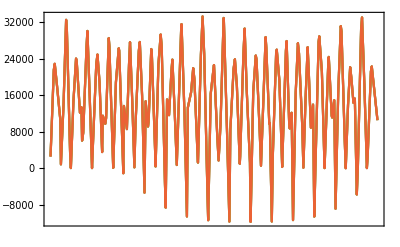

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,1]]}],100]&,{time,core}]]
```

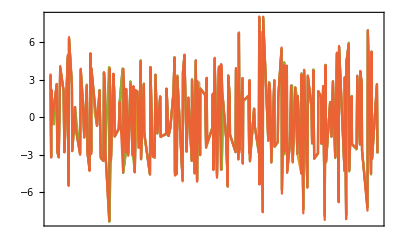

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,1]]}],100]&,{time,crust}]]
```

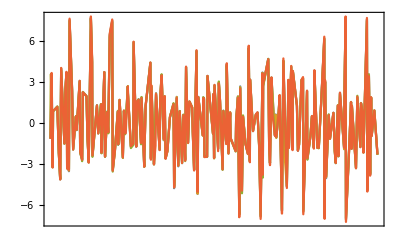

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,2]]}],100]&,{time,crust}]]
```

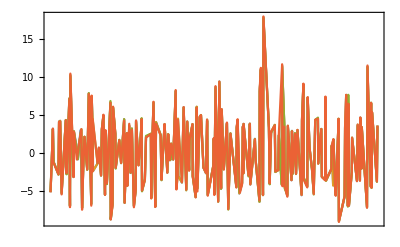

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,3]]}],100]&,{time,crust}]]
```

```mathematica
{{"N","E","C"}}~Join~((c↦StandardDeviation/@Transpose[c])/@crust)//TableForm
```

N | E | C
1.62539 | 1.47335 | 2.26769
1.62706 | 1.4725 | 2.26891
1.62101 | 1.46584 | 2.25845
1.64238 | 1.48372 | 2.28842

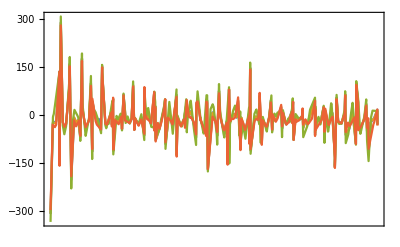

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,1]]}],100]&,{time,dbmeas}],PlotRange->All]
```

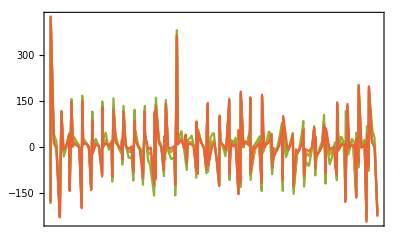

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,2]]}],100]&,{time,dbmeas}],PlotRange->All]
```

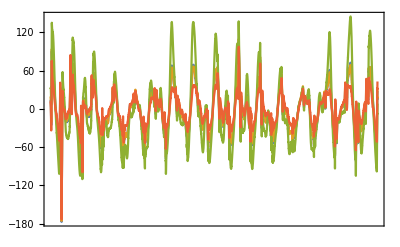

```mathematica
DateListPlot[MapThread[deleteRedundantPoints[Transpose[{#1,#2[[All,3]]}],1000]&,{time,dbmeas}],PlotRange->All]
```

```mathematica
ind=1;;4000;
```

```mathematica
im={{65,5},{35,5}};
```

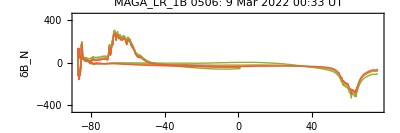

```mathematica
n=ListLinePlot[MapThread[Transpose[{#1[[ind]],#2[[ind,1]]}]&,{lat,dbmeas}],Frame->True,PlotRange->{-450,450},PlotStyle->AbsoluteThickness[1],PlotLabel->Row[{"MAGA_LR_1B 0506: ",DateString[Mean[time[[1,ind]]],{"DayShort"," ","MonthNameShort"," ","Year"," ","Hour24",":","Minute"," UT"}]}],FrameLabel->{"ITRF Latitude (°)","δB_N"},AspectRatio->1/3,ImagePadding->im,ImageSize->400]
```

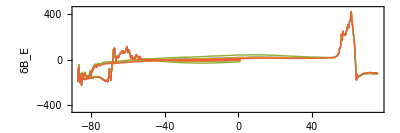

```mathematica
e=ListLinePlot[MapThread[Transpose[{#1[[ind]],#2[[ind,2]]}]&,{lat,dbmeas}],Frame->True,PlotRange->{-450,450},PlotStyle->AbsoluteThickness[1],FrameLabel->{"ITRF Latitude (°)","δB_E"},AspectRatio->1/3,ImagePadding->im,ImageSize->400]
```

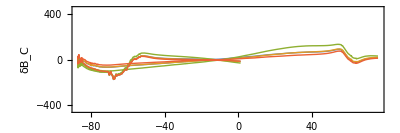

```mathematica
c=ListLinePlot[MapThread[Transpose[{#1[[ind]],#2[[ind,3]]}]&,{lat,dbmeas}],PlotLegends->versions,Frame->True,PlotRange->{-450,450},PlotStyle->AbsoluteThickness[1],FrameLabel->{"ITRF Latitude (°)","δB_C"},AspectRatio->1/3,ImagePadding->im,ImageSize->400]
```

```mathematica
plot=Column[{n,e,c}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
savePlot["SwarmA_B_NEC_residual_examples_CHAOS_7.9-to-7.12.png",plot]
```

/Users/john/src/chaos/Mathematica/SwarmA_B_NEC_residual_examples_CHAOS_7.9-to-7.12.png

```mathematica
SystemOpen@%
```